# ARTIQ DATA PROCESSING

## Last Updated: 2025/10/18 v1.1.1

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

```mathematica
(*todo: add rabi/FSD to this*)
```

# General

## Imports

```mathematica
(*memory management etc*)
Needs["Utilities`CleanSlate`"];
```

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

## Options

```mathematica
(*set analytical plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogLogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set list plot options*)
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set bar/histogram plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[BarChart,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Plot Creation

```mathematica
(*get default plot colors*)
DefaultPlotColors=Cases[#,_?ColorQ,All]&["DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[Automatic,Plot])];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

## Phonon Conversion

### Coherent_C

```mathematica
(*coherent_c: convert R/B ratio to <n> assuming a coherent state*)
```

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
CoherentCErr[x_]:=CoherentCFunc'[#]&[Clip[x,{0.,0.8}]];
```

### Coherent_R

```mathematica
(*coherent_c: convert RSB probability ONLY to <n> assuming a coherent state*)
```

```mathematica
coherentR0={
0,9.99931658497433*^-5,0.000399890663733249,0.000899446570690410,0.00159825126849689,0.00249573182347329,0.00359115251770981,0.00488361553119066,0.00637206177417027,0.00805527186899924,0.00993186728045770,0.0120003115935124,0.0142589119372707,0.0167058205537671,0.0193390365100727,0.0221564075520917,0.0251556320982592,0.0283342613712326,0.0316897016655309,0.0352192167489441,0.0389199303954148,0.0427888290469539,0.0468227646020514,0.0510184573278918,0.0553724988935951,0.0598813555215709,0.0645413712539629,0.0693487713310517,0.0742996656783876,0.0793900524992962,0.0846158219693280,0.0899727600291077,0.0954565522719444,0.101062787922491,0.106786963902628,0.112624488980697,0.118570688000088,0.124620806183157,0.130770013506336,0.137013409142264,0.143346025964675,0.149762835111746,0.156258750603538,0.162828634009109,0.169467299158846,0.176169516897511,0.182930019873458,0.189743507359448,0.196604650100454,0.203508095183842,0.210448470927264,0.217420391779606,0.224418463230326,0.231437286722481,0.238471464564783,0.245515604837990,0.252564326290965,0.259612263221736,0.266654070338924,0.273684427598902,0.280698045014097,0.287689667427855,0.294654079251349,0.301586109158018,0.308480634731091,0.315332587059793,0.322136955279870,0.328888791054132,0.335583212988793,0.342215410981400,0.348780650496278,0.355274276763424,0.361691718896910,0.368028493928910,0.374280210755539,0.380442573990817,0.386511387725119,0.392482559184592,0.398352102288109,0.404116141098438,0.409770913164383,0.415312772750811,0.420738193953524,0.426043773696107,0.431226234605960,0.436282427766861,0.441209335345508,0.446004073089648,0.450663892695473,0.455186184042142,0.459568477291385,0.463808444850291,0.467903903195516,0.471852814557270,0.475653288461590,0.479303583129547,0.482802106732168,0.486147418499979,0.489338229686260,0.492373404383192,0.495251960190268,0.497973068734440,0.500536056041652,0.502940402759546,0.505185744231242,0.507271870420298,0.509198725687029,0.510966408416576,0.512575170499202,0.514025416663485,0.515317703663170,0.516452739318639,0.517431381414049,0.518254636451358,0.518923658262584,0.519439746481792,0.519804344878417,0.520019039553689,0.520085557002049,0.520005762039560,0.519781655601477,0.519415372411236,0.518909178523259,0.518265468742100,0.517486763920557,0.516575708139507,0.515535065772334,0.514367718436921,0.513076661838286,0.511665002505056,0.510135954423077,0.508492835569525,0.506739064351023,0.504878155949329,0.502913718578252,0.500849449655556,0.498689131893661,0.496436629313061,0.494095883182420,0.491670907889407,0.489165786746364,0.486584667734993,0.483931759194270,0.481211325455891,0.478427682431564,0.475585193156511,0.472688263293616,0.469741336602651,0.466748890379059,0.463715430866808,0.460645488649837,0.457543614026645,0.454414372372584,0.451262339494410,0.448092096981688,0.444908227559604,0.441715310447763,0.438517916729525,0.435320604736432,0.432127915452247,0.428944367941117,0.425774454804329,0.422622637670119,0.419493342720928,0.416390956262505,0.413319820339149,0.410284228399400,0.407288421016389,0.404336581667029,0.401432832574140,0.398581230615570,0.395785763304283,0.393050344843310,0.390378812259402,0.387774921619125,0.385242344331059,0.382784663537692,0.380405370600468,0.378107861681413,0.375895434424601,0.373771284740682,0.371738503697539,0.369800074520074,0.367958869701985,0.366217648232303,0.364579052939329,0.363045607954507,0.361619716298632,0.360303657592692,0.359099585895489,0.358009527670097,0.357035379881037,0.356178908223974,0.355441745489547,0.354825390062886,0.354331204560147,0.353960414603333,0.353714107734502,0.353593232470306,0.353598597497709,0.353730871011554};
```

```mathematica
coherentRX0=Range[0.,2.,2./(Length[coherentR0]-1)]^2.;
```

```mathematica
(*note: need to truncate after 120 points b/c curve is non-injective after that*)
CoherentRFunc=Interpolation[Transpose[{coherentR0,coherentRX0}][[;;120]]];
CoherentR[x_]:=CoherentRFunc[#]&[Clip[x,{0.,0.6}]];
```

### Coherent_ARP

```mathematica
(*todo: account for n != 0*)
CoherentARP[P_,n_:0]:=-Log[P+1.*^-7];
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Threshold Counts

```mathematica
(*threshold counts into s-state vs d-state probability*)
Clear[ThresholdCounts];
Options[ThresholdCounts]={
"Threshold"->-1
};
```

```mathematica
(*implement threshold counts!*)
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

### Collate Data

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
Clear[CollateData,ftmpdj];
ftmpdj[arg_]:=N[Mean[arg]];
Options[CollateData]={
(*"ProcessFunction"->N[Mean[#]]&*)
"ProcessFunction"->ftmpdj
};

(*implement collate data!*)
CollateData[
dataset_List,
groupColumnList_List,
OptionsPattern[]
]:=With[{fdj=OptionValue["ProcessFunction"]},

Return[
GroupBy[
(*group dataset by nested columns*)
dataset,

(*create a table of functions for grouping by*)
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],

(*process grouped results with function*)
fdj[#]&
]//KeySort
];
];
```

### Collate Data Simple

```mathematica
(*implement collate data - simple!*)
Clear[CollateDataSimple];
CollateDataSimple[dataset_List,groupColumnList_List]:=Module[
{procFuncDJ,dsDJ},

(*organize data by sweep column(s)*)
procFuncDJ[data_]:=data;
dsDJ=CollateData[
dataset,
groupColumnList,
"ProcessFunction"->procFuncDJ
];

(*(*replace 0 uncertainty with 0.01*)
dsDJ[[;;,3]]=dsDJ[[;;,3]]/.{(0|0.)->0.01};*)

Return[KeyValueMap[
{#1,Mean[#2[[;;,2]]],StandardDeviation[#2[[;;,2]]]/(√Length[#2[[;;,2]]])}&,
dsDJ
]];
];
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

# User Input

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2026-06\\2026-07-27";
(*directoryString="/Users/claytonho/Documents/Research/Projects/Correlation Sampling/Data/2025_09_fock_lineshape";*)
```

## Validate User Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

# Run

## Fock Amplification Linescan

```mathematica
(*specify datasets*)
ridList={137540};(*list of RIDs*)
```

## Configuration

Dataset Configuration:

```mathematica
countCol=2;(*raw count column*)
```

```mathematica
sweepCol=4;(*sweep column*)
```

Convert Units:

```mathematica
sweepUnits=1.*^-3;(*convert from sweep column to target units*)
```

Processing Configuration:

```mathematica
α0DJ=√0.086;(*displacement of the n=0 state*)
```

Plotting Configuration:

```mathematica
xAxisLabel="Frequency (kHz)";(*x-axis label for sweep*)
```

```mathematica
figureTitle="Fock Linescan";(*plot title to set*)
```

## Import

```mathematica
(*import raw dataset*)
datafileList=ImportDatasetARTIQ[directoryString,ToString[#]]&/@ridList;
```

$Aborted

```mathematica
(*merge datasets and get parameter list*)
dataset=Join@@(First/@datafileList);
parameters=(First@datafileList)[[2]];
```

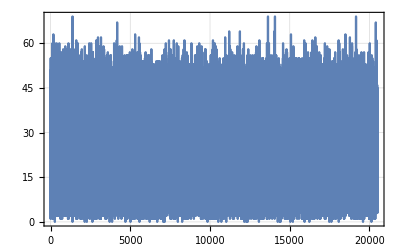
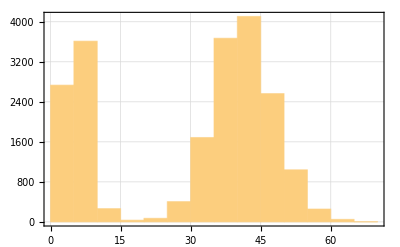
{(-1. | 9. | 8.6×10^7 | 600. | 0. | 0. | 1. | 0.1561 | 256.
-1. | 47. | 8.6×10^7 | 2400. | 0. | 0. | 1. | 0.1561 | 256.
-1. | 38. | 8.6×10^7 | 3200. | 0. | 0. | 1. | 0.1561 | 256.),-Graphics-,-Graphics-}

```mathematica
(*plot important stuff*)
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

```mathematica
(*get fock state*)
nDJ=parameters["fock_num_prep"];
(*guess pulse time*)
tPulseus=parameters["time_heating_us"]+0.5*parameters["time_pulse_shape_rolloff_us"]*parameters["enable_pulse_shaping"];
```

```mathematica
(*get empirical fidelity scaling factors*)
{ADJFix,CDJFix}=Switch[nDJ,
0,
{0.926687,0.0059494},
1,
{0.79492,0.077884},
2,
{0.72353,0.117476},
3,
{0.619214,0.18123}
];
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{sweepCol,countCol}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{sweepUnits,1}];
```

```mathematica
(*organize data by sweep column(s)*)
dsDJ=CollateDataSimple[
datasetProcessed[[;;,{1,2}]],
{1}
];
(*replace 0 uncertainty with 0.01*)
dsDJ[[;;,3]]=dsDJ[[;;,3]]/.{(0|0.)->0.01};
```

```mathematica
(*assign dataset for processing*)
dsN=dsDJ;
(*dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];*)
```

```mathematica
(*create datasets for plotting*)
dsRawPlot=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];
```

## Fit

### Prepare Fitting

```mathematica
(*fit function*)
(*note: requires fit with n=0 to get α0*)
fitfunc=ADJ*(1.-Exp[-#^2.]*LaguerreL[nDJ,#^2]^2.)+CDJ&[
α0*Sinc[((δ-δ0)*tDJ)/2.*(wkhz*μs)+1.*^-8]
];
```

```mathematica
(*fix extra parameters*)
(*fitfunc=fitfunc/.{α0->α0DJ};*)
(*fitfunc=fitfunc/.{ADJ->ADJFix,CDJ->CDJFix};*)
```

```mathematica
(*set fitting constraints*)
fitConstraintsDJ={
0.<=ADJ<=1.,
0.<=CDJ<=1.
};
```

```mathematica
(*guess fit parameters*)
fitGuessDJ={
{α0,-Log[1.-Abs[Subtract@@MinMax[dsN[[;;,2]]]]]},
{ADJ,1.-Min[dsN[[;;,2]]]},(*probability contrast*)
{CDJ,Min[dsN[[;;,2]]]},(*probability offset*)
{tDJ,tPulseus},(*pulse time*)
{δ0,First@dsN[[Ordering[dsN[[;;,2]],-1],1]]}(*linecenter*)
}
```

{{α0,0.848632},{ADJ,0.832},{CDJ,0.168},{tDJ,525.},{δ0,0.}}

```mathematica
(*extract weights*)
fitWeights=dsDJ[[;;,3]]^-2.;
```

### Fit & Extract Results

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN[[;;,{1,2}]],
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
δ,
Weights->fitWeights
];
]
```

{0.0218391,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

### Plot Fit

```mathematica
(*plot fitted results*)
fitPlot=Plot[
fitRes[δ],
{δ,dsN[[1,1]],dsN[[-1,1]]},
PlotRange->Full
];
```

### Plot Data

```mathematica
(*plot processed data*)
dataProcPlot=ListPlot[
{
dsRawPlot
},
PlotRange->{
{Full,Full},
{0.,1.}
},

FrameLabel->{ 
{Style["D-5/2 Probability",{Black,Directive[15]}],None},
{
Style[xAxisLabel,{Black,Directive[15]}],
Style[StringForm[
"`` - RID: ``, n=``\nPulse Time: ``μs, Linecenter Precision: `` Hz",
figureTitle,ridList,nDJ,parameters["time_heating_us"],NumberForm[Abs[1000.*Subtract@@fitRes["ParameterConfidenceIntervals"][[-1]]],5]
],{Black,Directive[15]}]
}
},

PlotStyle->{Black},
ImageSize->{700,450},
AspectRatio->Full
];
```

### Create Summary Figure

```mathematica
(*plot summary figure*)
summaryFigure=Show[
{
dataProcPlot,
fitPlot
}
];
```

## Show

Linecenter Precision: 57.167 Hz

| Estimate | Standard Error | Confidence Interval
α0 | 0.358752 | 0.0538367 | {0.249567,0.467938}
ADJ | 0.81394 | 0.169857 | {0.469453,1.15843}
CDJ | 0.192195 | 0.00354531 | {0.185004,0.199385}
tDJ | 520.247 | 11.5712 | {496.779,543.714}
δ0 | 0.139655 | 0.0140939 | {0.111071,0.168238}

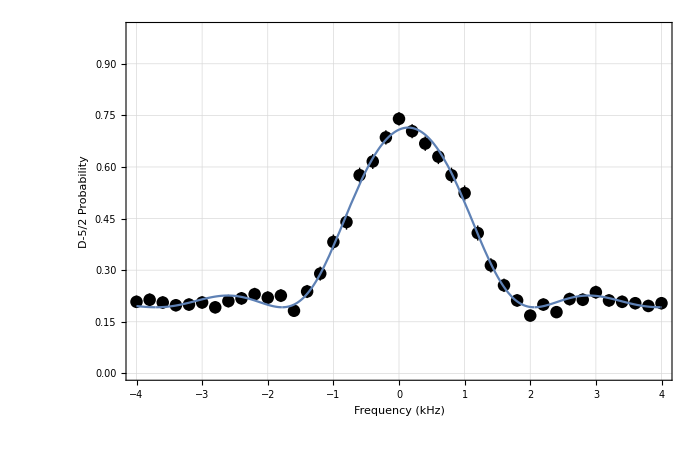

```mathematica
Print[StringForm["Linecenter Precision: `` Hz",NumberForm[Abs[1000.*Subtract@@fitRes["ParameterConfidenceIntervals"][[-1]]],5]]];
fitParams
summaryFigure
```

```mathematica
RandomSample[{}]
```

```mathematica
RandomInteger[{1,35},3]
```

{1,28,8}

## General Phase Sweep

```mathematica
(*specify datasets*)
ridList={161292};(*list of RIDs*)
```

## Configuration

Dataset Configuration:

```mathematica
freqReadoutCol=1;(*729nm readout freq - used for SBR readout*)
```

```mathematica
countCol=2;(*raw count column*)
```

```mathematica
sweepCol =13; 5;9;5;3;8;(*sweep column*)(*10 for QVSA phase, 5 for Cat2 phase*)
```

Convert Units:

```mathematica
freqReadoutUnits=1;ftwToFrequencyMHz;(*convert from readout frequency to target units*)
(*freqReadoutUnits =1;*)
```

```mathematica
sweepUnits=1.;1./(2.^16.-1.);(*ftwToFrequencyMHz*10^3*)1./(2.^16.-1.);1/65600*1/0.965716;(*convert from sweep column to target units*)(*1 for QVSA phase, 1./(2.^16.-1.) for cat2 phase*)
```

Processing Configuration:

```mathematica
procStyle="729";(*sideband ratio: "SBR", RAP: "RAP", 729: "729"*)
```

```mathematica
periodicity=1.;(*number of oscillations*)
```

Plotting Configuration:

```mathematica
xAxisLabel="Phase (Turns)";(*x-axis label for sweep*)
figureTitle="SDR Calib";(*plot title to set*)
(*figureTitle="Parity Pulse After Pi Pulse.";(*plot title to set*)*)
```

## Import

```mathematica
(*import raw dataset*)
datafileList=ImportDatasetARTIQ[directoryString,ToString[#]]&/@ridList;
```

```mathematica
(*merge datasets and get parameter list*)
dataset=Join@@(First/@datafileList);
parameters=(First@datafileList)[[2]];
```

Join::normal: Nonatomic expression expected at position 1 in Join[Z:\motion\Data\2026-06\2026-06-17].

```mathematica
(*plot important stuff*)
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["enable_antisqueezing"]*)
};
```

Part::partd: Part specification Join[Z:\motion\Data\2026-06\2026-06-17]⟦1;;All,2⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 3 in Join[Z:\motion\Data\2026-06\2026-06-17].

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: Join[Z:\motion\Data\2026-06\2026-06-17]⟦1;;All,2⟧ is not a list of numbers or pairs of numbers.

## Process

### Preprocess

```mathematica
(*threshold counts (via auto histogram-based method)*)
datasetProcessed=ThresholdCounts[
dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],
3
];

(*convert dataset units*)
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{freqReadoutUnits,sweepUnits,1}
];
```

```mathematica
(*(*phase unwrap*)
dsR[[;;,1]]=Mod[dsR[[;;,1]],1,-0.5];
dsB[[;;,1]]=Mod[dsB[[;;,1]],1,-0.5];*)
(*(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];*)
```

```mathematica
(*(*phase unwrap & sort*)
datasetProcessed[[;;,1]]=Mod[datasetProcessed[[;;,1]],1,-0.5];
datasetProcessed=SortBy[datasetProcessed,First];*)
```

### Configured Processing

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=CollateDataSimple[#,{1}]&/@{dsR,dsB};

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsR[[;;,3]]=dsR[[;;,3]]/.{(0|0.)->0.01};
	dsR=Transpose[{dsR[[;;,1]],Around@@@dsR[[;;,{2,3}]]}];
	dsB[[;;,3]]=dsB[[;;,3]]/.{(0|0.)->0.01};
	dsB=Transpose[{dsB[[;;,1]],Around@@@dsB[[;;,{2,3}]]}];

	(*process phonon number*)
	dsN=dsR;dsN[[;;,2]]/=dsB[[;;,2]];
	dsNValTMP=CoherentC[#["Value"]&/@dsN[[;;,2]]];
	dsNErrTMP=CoherentCErr[#["Uncertainty"]&/@dsN[[;;,2]]];
	dsNErrTMP=(#*CoherentCErr[#])&/@(#["Uncertainty"]&/@dsN[[;;,2]]);

	(*final plotting preparation*)
	dsRawPlot={dsR,dsR,dsB,dsB};
	dsConfiguredYLabel="⟨n⟩";,

"RAP",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];
	dsConfiguredYLabel="⟨n⟩";,

"729",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsConfiguredYLabel="Dark-State Probability (P_D)";
];
```

## Fit

```mathematica
(*separate out values from uncertainty (b/c fit functions can't take Around)*)
dsFitVals={#[[1]],#[[2]]["Value"]}&/@dsN;
dsFitWeights=(#[[2]]["Uncertainty"]&/@dsN)^-2.;
```

### Prepare Fitting

```mathematica
(*fit function*)
fitfunc=α*Cos[(periodicity*1.*π)*(ϕ-ϕ0)]^2.+δ;
(*fitConstraintsDJ={α>0.,0.5>=ϕ0>=-0.5,δ>0.};*)
fitConstraintsDJ={δ>0.,-1.<=ϕ0<=1.};
```

```mathematica
(*guess fit values*)
fitGuessDJ={
{α,Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]/2.},
{ϕ0,0.5-First@dsFitVals[[Ordering[dsFitVals[[;;,2]],-1],1]]},
{δ,Min[dsFitVals[[;;,2]]]+Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]/4.}
}
```

{{α,0.295682},{ϕ0,-0.38},{δ,0.216834}}

### Fit & Extract Results

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsFitVals,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
ϕ,
Weights->dsFitWeights
];
]
```

{0.0164026,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

### Raw Data

```mathematica
(*raw probability plot*)
dataProbPlot=ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Red,PointSize[0.015]},
{Red,Dashed,Thickness[0.004]},
{Blue,PointSize[0.015]},
{Blue,Dashed,Thickness[0.004]}
},
Joined->{False,True,False,True},
ImageSize->Scaled[0.45]
];
```

### Processed Data

```mathematica
(*phonon plot*)
dataPhononPlot=ListPlot[
{
dsN,dsN
},
PlotRange->{
{Automatic,Automatic},
{0,Automatic(*Full*)}
},
FrameLabel->{ 
{Style[dsConfiguredYLabel,{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

### Fit Results

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

### Summary Figure

```mathematica
(*combine summary figure*)
summaryFigure={
(*processed data*)
Show[{
dataPhononPlot,
fitPlot
}
],
dataProbPlot
};
```

## Show

```mathematica
(*dataPhononPlot1 = dataPhononPlot;*)
```

| Estimate | Standard Error | Confidence Interval
α | 0.321833 | 0.0553452 | {0.207343,0.436323}
ϕ0 | -0.0949272 | 0.0253154 | {-0.147296,-0.0425583}
δ | 0.12817 | 0.0265682 | {0.0732097,0.183131}

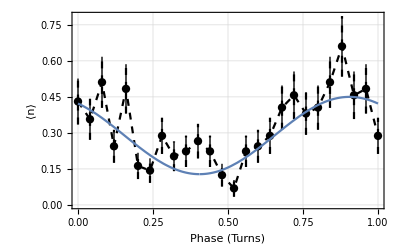
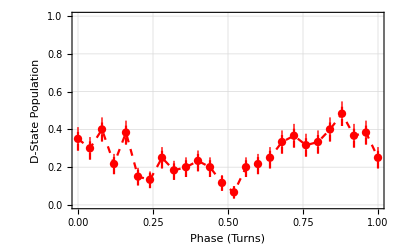

```mathematica
fitParams
summaryFigure
```

```mathematica
.1693-0.0949
```

0.0744

```mathematica
0.1563-(1.-0.899272)
```

0.055572

## General Ramsey Sweep

```mathematica
(*todo: fix ramsey fitting*)
```

```mathematica
(*specify datasets*)
ridList={139934};(*list of RIDs*)
```

## Configuration

Dataset Configuration:

```mathematica
freqReadoutCol=1;(*729nm readout freq - used for SBR readout*)
```

```mathematica
countCol=2;(*raw count column*)
```

```mathematica
sweepCol=1;8;(*sweep column*)(*Column 1: carrier, Column 3: secular, Column 8: Delay time*)
```

Convert Units:

```mathematica
freqReadoutUnits=ftwToFrequencyMHz*10^3;1*10^-1;(*convert from readout frequency to target units*)
```

```mathematica
sweepUnits=ftwToFrequencyMHz*10^3;1*10^-3;1/kHz;ftwToFrequencyMHz*kHz; 1*10^-3;(*convert from sweep column to target units*)
```

Processing Configuration:

```mathematica
procStyle="729";(*sideband ratio: "SBR", RAP: "RAP", 729: "729"*)
```

```mathematica
fitStyle="COS";(*full ramsey fit: "RAM", cosine-only fit: "COS"*)
timeFudgeUS=0.;(*adjust if bad fit: ~100 for small delay tims (~100us), ~0 for long delays (~1000us)*)
```

```mathematica
(*"RAM" fit parameters*)
freqScale=1.*^0;(*axis scale for the "RAM"/ramsey fit option*)
timeHeatUS=6.6;(*ramsey pulse time*)
timeDelayUS=500;(*ramsey delay time*)
```

```mathematica
(*"COS" fit parameters*)
ϕFitDJ=0.5;(*phase offset for fitting*)
timeRamseyUS=2500.;(*ramsey delay time*)
```

Plotting Configuration:

```mathematica
xAxisLabel= "Frequency (kHz)" ;(*x-axis label for sweep*)
```

```mathematica
figureTitle="Ramsey Freq. Sweep";(*plot title to set*)
```

## Import

```mathematica
(*import raw dataset*)
datafileList=ImportDatasetARTIQ[directoryString,ToString[#]]&/@ridList;
```

```mathematica
(*merge datasets and get parameter list*)
dataset=Join@@(First/@datafileList);
parameters=(First@datafileList)[[2]];
```

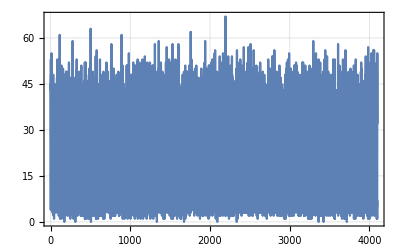
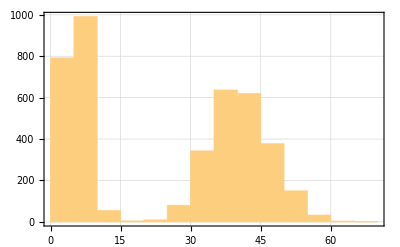
{(4.34105×10^8 | 45. | 1.×10^7 | 0. | 0.
4.34104×10^8 | 43. | 1.×10^7 | 0. | 0.
4.34104×10^8 | 4. | 1.×10^7 | 0. | 0.),-Graphics-,-Graphics-}

```mathematica
(*plot important stuff*)
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["enable_antisqueezing"]*)
};
```

## Process

### Preprocess

```mathematica
(*threshold counts (via auto histogram-based method)*)
datasetProcessed=ThresholdCounts[
dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],
3
];

(*convert dataset units*)
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{freqReadoutUnits,sweepUnits,1}
];
```

```mathematica
(*subtract mean*)
tha=Mean[datasetProcessed[[;;,1]]];
datasetProcessed[[;;,1]]-=Mean[datasetProcessed[[;;,1]]];
datasetProcessed[[;;,2]]-=Mean[datasetProcessed[[;;,2]]];
```

```mathematica
(*(*Adjust for carrier offset: offset is 101.074035*)
datasetProcessed=Table[{datasetProcessed[[ii,1]],datasetProcessed[[ii,2]]-101074.035,datasetProcessed[[ii,3]]},{ii,1,Length[datasetProcessed[[;;,1]]]}]*)
```

### Configured Processing

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=CollateDataSimple[#,{1}]&/@{dsR,dsB};

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsR[[;;,3]]=dsR[[;;,3]]/.{(0|0.)->0.01};
	dsR=Transpose[{dsR[[;;,1]],Around@@@dsR[[;;,{2,3}]]}];
	dsB[[;;,3]]=dsB[[;;,3]]/.{(0|0.)->0.01};
	dsB=Transpose[{dsB[[;;,1]],Around@@@dsB[[;;,{2,3}]]}];

	(*process phonon number*)
	dsN=dsR;dsN[[;;,2]]/=dsB[[;;,2]];
	dsNValTMP=CoherentC[#["Value"]&/@dsN[[;;,2]]];
	dsNErrTMP=CoherentCErr[#["Uncertainty"]&/@dsN[[;;,2]]];
	dsNErrTMP=(#*CoherentCErr[#])&/@(#["Uncertainty"]&/@dsN[[;;,2]]);

	(*final plotting preparation*)
	dsRawPlot={dsR,dsR,dsB,dsB};
	dsConfiguredYLabel="⟨n⟩";,

"RAP",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];
	dsConfiguredYLabel="⟨n⟩";,

"729",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsConfiguredYLabel="Dark-State Probability (P_D)";
];
```

## Fit

```mathematica
(*separate out values from uncertainty (b/c fit functions can't take Around)*)
dsFitVals={#[[1]],#[[2]]["Value"]}&/@dsN;
dsFitWeights=(#[[2]]["Uncertainty"]&/@dsN)^-2.;
```

### Prepare Ramsey Fit

```mathematica
(*create full ramsey fit function*)
fitfuncRAM=α*Sinc[(2.*π*freqScale)((x-β)*τ)/2.+1.*^-5]^2.*
Sin[(2.*π*freqScale)*(((x-β)*(T+τ))/2.)+(2.*π*ϕ)]^2.+
δ;
```

```mathematica
(*tmp remove*)
fitfuncRAM=fitfuncRAM/.{ϕ->ϕFitDJ};
```

```mathematica
(*ramsey constraints*)
fitConstraintsRAM={
α>0.,
(*0.5>=ϕ>=-0.5,*)
δ>0.
};
```

```mathematica
fitGuessRAM={
{α,Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]},(*amplitude*)
{β,First@dsN[[Ordering[dsFitVals[[;;,2]],-1],1]]},(*linecenter*)
(*{ϕ,ϕFitDJ},(*phase shift*)*)
{T,(timeDelayUS+timeFudgeUS)*1.*^-3},(*delay time*)
{τ,timeHeatUS*1.*^-3},(*pulse time*)
{δ,Min[dsFitVals[[;;,2]]]}(*offset*)
}
```

{{α,0.66},{β,-0.400009},{T,0.5},{τ,0.0066},{δ,0.13}}

### Prepare Cosine Fit

```mathematica
(*cosine fit function - pretty straightforward*)
fitfuncCOS=α*Cos[(T*1.*π)*(x-x0)]^2.+δ;
```

```mathematica
(*cosine fit constraints - pretty straightforward*)
fitConstraintsCOS={
α>0.,
(*0.5>=ϕ0>=-0.5,*)
δ>0.
};
```

```mathematica
(*cosine fit guesses*)
fitGuessCOS={
(*guess ampl as max-min*)
{α,Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]},

(*guess ramsey time via user arguments lol(note: convert to ms b/c idk)*)
{T,(timeRamseyUS+timeFudgeUS)*1.*^-3},

(*guess offset as min val*)
{δ,Min[dsFitVals[[;;,2]]]},

(*guess zero phase reference as phase of the max point*)
{x0,First@dsN[[Ordering[dsFitVals[[;;,2]],-1],1]]}
}
```

{{α,0.66},{T,2.5},{δ,0.13},{x0,-0.400009}}

### Fit & Extract Results

```mathematica
(*select target fit styles*)
Switch[fitStyle,

"COS",
	fitfuncDJ=fitfuncCOS;
	fitConstraintsDJ=fitConstraintsCOS;
	fitGuessDJ=fitGuessCOS;,

"RAM",
	fitfuncDJ=fitfuncRAM;
	fitConstraintsDJ=fitConstraintsRAM;
	fitGuessDJ=fitGuessRAM;
]
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsFitVals,
Join[{fitfuncDJ},fitConstraintsDJ],
fitGuessDJ,
x,
Weights->dsFitWeights
];
]
```

{0.0102319,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

### Raw Data

```mathematica
(*raw probability plot*)
dataProbPlot=ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0,Automatic}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Red,PointSize[0.015]},
{Red,Dashed,Thickness[0.004]},
{Blue,PointSize[0.015]},
{Blue,Dashed,Thickness[0.004]}
},
Joined->{False,True,False,True},
ImageSize->Scaled[0.45]
];
```

### Processed Data

```mathematica
(*phonon plot*)
dataPhononPlot=ListPlot[
{
dsN,dsN
},
PlotRange->{
{Automatic, Automatic},
{0,1.}
(*{0.,(*Automatic*)(*Full*)1.}*)
},
FrameLabel->{ 
{Style[dsConfiguredYLabel,{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

### Fit Results

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

### Summary Figure

```mathematica
(*combine summary figure*)
summaryFigure={
(*processed data*)
Show[{
dataPhononPlot,
fitPlot
}
],
dataProbPlot
};
```

## Show

```mathematica
NumberForm[tha+fitParams[[1]][[1]][[3]][[2]],{∞,7}]
```

101075.3423905

| Estimate | Standard Error | Confidence Interval
α | 0.604442 | 0.0217698 | {0.560332,0.648552}
T | 2.24236 | 0.00519194 | {2.23184,2.25288}
δ | 0.150302 | 0.012733 | {0.124502,0.176101}
x0 | -0.373495 | 0.00292106 | {-0.379414,-0.367576}

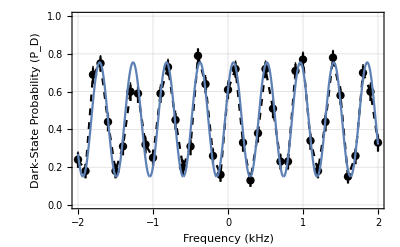
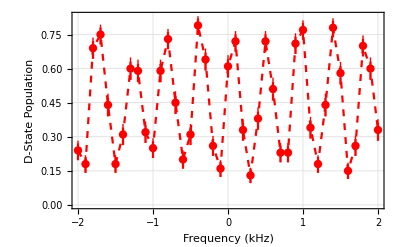

```mathematica
fitParams
summaryFigure
```

## General Heating Rate

```mathematica
(*specify datasets*)
ridList={158239};(*list of RIDs*)
```

## Configuration

Dataset Configuration:

```mathematica
freqReadoutCol=1;(*729nm readout freq - used for SBR readout*)
```

```mathematica
countCol=2;(*raw count column*)
```

```mathematica
sweepCol=3;(*sweep column*)
```

Convert Units:

```mathematica
freqReadoutUnits=ftwToFrequencyMHz;(*convert from readout frequency to target units*)
```

```mathematica
sweepUnits=1.*ns/ms;100./(2^14-1);ftwToFrequencyMHz*1.*^3;100./(2^14-1);100./(2^14-1);ftwToFrequencyMHz*1.*^3;1.*ns/μs;ftwToFrequencyMHz;1.*^0*60;(*convert sweep column to target units*)
```

Processing Configuration:

```mathematica
procStyle="THERMAL";"RAP";(*sideband ratio: "SBR", RAP: "RAP", thermal (RAP-based): "THERMAL" 729: "729"*)
```

Plotting Configuration:

```mathematica
(*xAxisLabel="Ampl. (%)";(*x-axis label for sweep*)
figureTitle="SBC Quench Opt. - AX";(*plot title to set*)*)
```

```mathematica
xAxisLabel="Wait Time (ms)";(*x-axis label for sweep*)
figureTitle="Heating Rate - AX";(*plot title to set*)
```

```mathematica
(*xAxisLabel="Beam Freq. (MHz)";(*x-axis label for sweep*)
figureTitle="SBC Calib - RF";(*plot title to set*)*)
```

## Import

```mathematica
(*import raw dataset*)
datafileList=ImportDatasetARTIQ[directoryString,ToString[#]]&/@ridList;
```

```mathematica
(*merge datasets and get parameter list*)
dataset=Join@@(First/@datafileList);
parameters=(First@datafileList)[[2]];
```

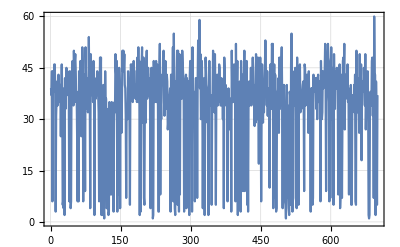
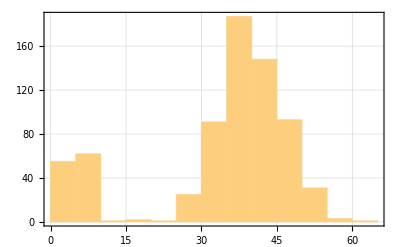
{(4.30104×10^8 | 39. | 5.×10^7
4.30104×10^8 | 37. | 1.×10^8
4.30104×10^8 | 44. | 3.×10^7),-Graphics-,-Graphics-}

```mathematica
(*plot important stuff*)
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["enable_antisqueezing"]*)
};
```

## Process

### Preprocess

```mathematica
(*threshold counts (via auto histogram-based method)*)
datasetProcessed=ThresholdCounts[
dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],
3
];

(*convert dataset units*)
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{freqReadoutUnits,sweepUnits,1}
];
```

### Configured Processing

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=CollateDataSimple[#,{1}]&/@{dsR,dsB};

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsR[[;;,3]]=dsR[[;;,3]]/.{(0|0.)->0.01};
	dsR=Transpose[{dsR[[;;,1]],Around@@@dsR[[;;,{2,3}]]}];
	dsB[[;;,3]]=dsB[[;;,3]]/.{(0|0.)->0.01};
	dsB=Transpose[{dsB[[;;,1]],Around@@@dsB[[;;,{2,3}]]}];

	(*process phonon number*)
	dsN=dsR;dsN[[;;,2]]/=dsB[[;;,2]];
	dsNValTMP=CoherentC[#["Value"]&/@dsN[[;;,2]]];
	dsNErrTMP=CoherentCErr[#["Uncertainty"]&/@dsN[[;;,2]]];
	dsNErrTMP=(#*CoherentCErr[#])&/@(#["Uncertainty"]&/@dsN[[;;,2]]);

	(*final plotting preparation*)
	dsRawPlot={dsR,dsR,dsB,dsB};
	dsConfiguredYLabel="⟨n⟩";,

"RAP",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];
	dsConfiguredYLabel="⟨n⟩";,

"THERMAL",
	(*collate dataset*)
	dsN=CollateDataSimple[datasetProcessed[[;;,{2,3}]],{1}];
	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/. {(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsN[[;;,2]]=1./(1.-dsN[[;;,2]])-1.;
	dsConfiguredYLabel="⟨n⟩";,

"729",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsConfiguredYLabel="Dark-State Probability (P_D)";
];
```

## Fit

```mathematica
(*separate out values from uncertainty (b/c fit functions can't take Around)*)
dsFitVals={#[[1]],#[[2]]["Value"]}&/@dsN;
dsFitWeights=(#[[2]]["Uncertainty"]&/@dsN)^-2.;
```

### Fit & Extract Results

```mathematica
(*fit linear model!*)
AbsoluteTiming[
fitRes=LinearModelFit[
dsFitVals,
{1,x},
x,

Weights->dsFitWeights
];
]
```

{0.0005747,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

### Raw Data

```mathematica
(*raw probability plot*)
dataProbPlot=ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Red,PointSize[0.015]},
{Red,Dashed,Thickness[0.004]},
{Blue,PointSize[0.015]},
{Blue,Dashed,Thickness[0.004]}
},
Joined->{False,True,False,True},
ImageSize->Scaled[0.45]
];
```

### Processed Data

```mathematica
(*phonon plot*)
dataPhononPlot=ListPlot[
{
dsN,dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,(*Automatic*)Full}
},
FrameLabel->{ 
{Style[StringForm["``",dsConfiguredYLabel],{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

### Fit Results

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

### Summary Figure

```mathematica
(*combine summary figure*)
summaryFigure={
(*processed data*)
Show[{
dataPhononPlot,
fitPlot
}
],
dataProbPlot
};
```

## Show

| Estimate | Standard Error | Confidence Interval
1 | 0.119079 | 0.0181683 | {0.0723759,0.165782}
x | 0.00134984 | 0.000314786 | {0.000540661,0.00215903}

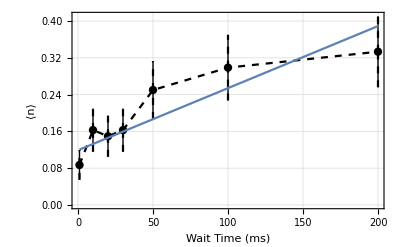
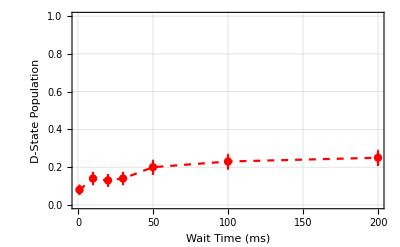

```mathematica
fitParams
summaryFigure
```

## Free Induction Decay

```mathematica
(*todo: maybe integrate with ramsey???*)
```

```mathematica
(*todo: guess decay time via filtering & log*)
```

```mathematica
(*specify datasets*)
directoryString="Z:\\motion\\Data\\2025-11\\2025-11-15";
ridList={140083};(*list of RIDs*)
```

```mathematica
ntmp=0;
```

## Configuration

Dataset Configuration:

```mathematica
freqReadoutCol=1;(*729nm readout freq - used for SBR readout*)
```

```mathematica
countCol=2;(*raw count column*)
```

```mathematica
sweepCol=6;(*sweep column*)
```

Convert Units:

```mathematica
freqReadoutUnits=ftwToFrequencyMHz;(*convert from readout frequency to target units*)
```

```mathematica
sweepUnits=1.*^-3;μs;(*convert sweep column to target units*)
```

Processing Configuration:

```mathematica
procStyle="729";(*sideband ratio:"SBR", RAP:"RAP", 729:"729"*)
```

```mathematica
ωGuess=6.;(*guess detuning (in x2π kHz)*)
```

```mathematica
τGuess=5.;(*guess decay time (in ms)*)
```

Plotting Configuration:

```mathematica
xAxisLabel="Time (ms)";(*x-axis label for sweep*)
```

```mathematica
figureTitle="Free Induction Decay";(*plot title to set*)
```

## Import

```mathematica
(*import raw dataset*)
datafileList=ImportDatasetARTIQ[directoryString,ToString[#]]&/@ridList;
```

```mathematica
(*merge datasets and get parameter list*)
dataset=Join@@(First/@datafileList);
parameters=(First@datafileList)[[2]];
```

```mathematica
(*ds2=dataset;
ds2[[;;,-1]]=Round/@ds2[[;;,-1]];
ds2=GroupBy[ds2,Last];
dataset=ds2[ntmp];
figureTitle=StringForm["Free Induction Decay (``)","n="<>ToString[ntmp]];*)
```

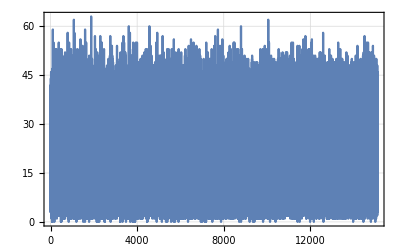
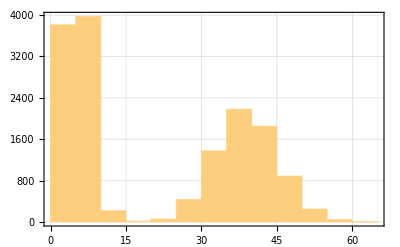
{(-1. | 5. | 8.6×10^7 | 4000. | 0. | 1252. | 1. | 0. | 256. | 0.
-1. | 6. | 8.6×10^7 | 4000. | 0. | 2468. | 1. | 0. | 256. | 0.
-1. | 4. | 8.6×10^7 | 4000. | 0. | 1684. | 1. | 0. | 256. | 0.),-Graphics-,-Graphics-}

```mathematica
(*plot important stuff*)
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["enable_antisqueezing"]*)
};
```

## Process

### Preprocess

```mathematica
(*threshold counts (via auto histogram-based method)*)
datasetProcessed=ThresholdCounts[
dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],
3
];

(*convert dataset units*)
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{freqReadoutUnits,sweepUnits,1}
];
```

### Configured Processing

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=CollateDataSimple[#,{1}]&/@{dsR,dsB};

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsR[[;;,3]]=dsR[[;;,3]]/.{(0|0.)->0.01};
	dsR=Transpose[{dsR[[;;,1]],Around@@@dsR[[;;,{2,3}]]}];
	dsB[[;;,3]]=dsB[[;;,3]]/.{(0|0.)->0.01};
	dsB=Transpose[{dsB[[;;,1]],Around@@@dsB[[;;,{2,3}]]}];

	(*process phonon number*)
	dsN=dsR;dsN[[;;,2]]/=dsB[[;;,2]];
	dsNValTMP=CoherentC[#["Value"]&/@dsN[[;;,2]]];
	dsNErrTMP=CoherentCErr[#["Uncertainty"]&/@dsN[[;;,2]]];
	dsNErrTMP=(#*CoherentCErr[#])&/@(#["Uncertainty"]&/@dsN[[;;,2]]);

	(*final plotting preparation*)
	dsRawPlot={dsR,dsR,dsB,dsB};
	dsConfiguredYLabel="⟨n⟩";,

"RAP",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];
	dsConfiguredYLabel="⟨n⟩";,

"729",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsConfiguredYLabel="Dark-State Probability (P_D)";
];
```

## Fit

```mathematica
(*separate out values from uncertainty (b/c fit functions can't take Around)*)
dsFitVals={#[[1]],#[[2]]["Value"]}&/@dsN;
dsFitWeights=(#[[2]]["Uncertainty"]&/@dsN)^-2.;
```

### Prepare Fit - With Offset

Fit function: exponentially damped cosine
Note: for this fit, y-axis offset IS a free parameter
Fit parameters:
A: amplitude
ω: oscillation/fringe frequency
τ: decay constant
t0: initial time/phase offset
C0: y-axis offset

```mathematica
(*(*prepare fit function*)
fitfuncDJ=(A*Exp[-(t/τ)^1.])/2.*Cos[(ω*1.*π)*(t-t0)]+COff;*)
```

```mathematica
(*(*specify fit constraints
note: the fewer constraints, the better*)
fitConstraintsDJ={
A>0.,
COff>0.,
τ>0.
};*)
```

```mathematica
(*(*guess parameters*)
fitGuessDJ={
{A,Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]},
{ω,ωGuess},
{τ,τGuess},
{t0,0.},
{COff,Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]/2.}
}*)
```

### Prepare Fit - No Offset (i.e. base case contrast SHOULD go to zero)

Fit function: exponentially damped cosine
Note: for this fit, y-axis offset is NOT free parameter, and is determined by the amplitude
Fit parameters:
A: amplitude
ω: oscillation/fringe frequency
τ: decay constant
t0: initial time/phase offset

```mathematica
(*(*prepare fit function*)
fitfuncDJ=A/2.(1.+Exp[-(t/τ)^1.]*Cos[(ω*1.*π)*(t-t0)]);*)
```

```mathematica
(*(*specify fit constraints
note: the fewer constraints, the better*)
fitConstraintsDJ={
A>0.,
τ>0.
};*)
```

```mathematica
(*(*guess parameters*)
fitGuessDJ={
{A,Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]},
{ω,ωGuess},
{τ,τGuess},
{t0,0.}
}*)
```

### Prepare Fit - Get Amplitude Only (No Decay)

Fit function: exponentially damped cosine
Note: for this fit, we ignore decay; just want to get the fringe amplitude
Fit parameters:
A: amplitude
ω: oscillation/fringe frequency
t0: initial time/phase offset
C0: y-axis offset

```mathematica
(*(*prepare fit function*)
fitfuncDJ=A/2.*Cos[(ω*1.*π)*(t-t0)]+COff;*)
```

```mathematica
(*(*specify fit constraints
note: the fewer constraints, the better*)
fitConstraintsDJ={
A>0.
};*)
```

```mathematica
(*(*guess parameters*)
fitGuessDJ={
{A,Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]},
{ω,ωGuess},
{t0,0.},
{COff,Abs[Subtract@@MinMax[dsFitVals[[;;,2]]]]/2.}
}*)
```

### Prepare Fit - Fock Special

```mathematica
(*get empirical fidelity scaling factors*)
{ADJFix, CDJFix} = Switch[ntmp,
   0,
   {0.926687, 0.0059494},
   1,
   {0.79492, 0.077884},
   2,
   {0.72353, 0.117476},
   3,
   {0.619214, 0.18123}
   ];
```

```mathematica
(*fit function*)
(*note: requires fit with n=0 to get α0*)
fitfuncDJ=ADJ*(1.-Exp[-#^2.]*LaguerreL[ntmp,#^2]^2.)+CDJ&[
α0*(1.+Exp[-(t/τ)]*Cos[(ω*1.*π)*(t-t0)])
];
```

```mathematica
(*fix extra parameters*)
(*fitfuncDJ=fitfuncDJ/.{α0->0.472};*)
(*fitfuncDJ=fitfuncDJ/.{ADJ->ADJFix,CDJ->CDJFix};*)
```

```mathematica
(*set fitting constraints*)
fitConstraintsDJ={
0.<=ADJ<=1.,
0.<=CDJ<=1.
};
```

```mathematica
(*guess fit parameters*)
fitGuessDJ={
{α0,0.4(*-Log[1.-Abs[Subtract@@MinMax[dsN[[;;,2]]]]]*)},
{ADJ,ADJFix(*1.-Min[dsFitVals[[;;,2]]]*)},(*probability contrast*)
{CDJ,CDJFix(*Min[dsFitVals[[;;,2]]]*)},(*probability offset*)
{ω,ωGuess},
{τ,τGuess},
{t0,0.}
}
```

{{α0,0.4},{ADJ,0.926687},{CDJ,0.0059494},{ω,6.},{τ,5.},{t0,0.}}

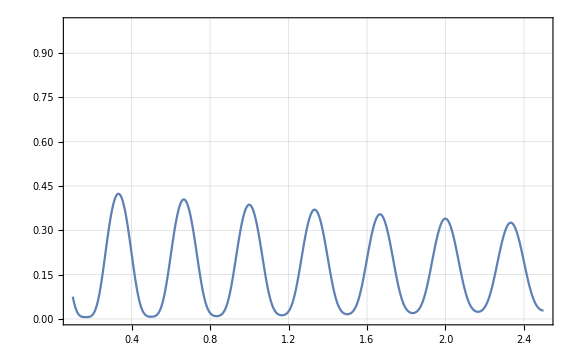

```mathematica
fscde[func_,appl_]:=func/. ({#1->#2}&@@appl);
funcfit2=Fold[fscde,fitfuncDJ,fitGuessDJ];
Plot[
funcfit2,
{t,dsFitVals[[1,1]],dsFitVals[[-1,1]]},
PlotRange->{
{Full,Full},
{0.,1.}
}
]
```

### Fit & Extract Results

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsFitVals,
Join[{fitfuncDJ},fitConstraintsDJ],
fitGuessDJ,
t,

Weights->dsFitWeights
];
]
```

{0.0331384,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

### Raw Data

```mathematica
(*raw probability plot*)
dataProbPlot=ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Red,PointSize[0.015]},
{Red,Dashed,Thickness[0.004]},
{Blue,PointSize[0.015]},
{Blue,Dashed,Thickness[0.004]}
},
Joined->{False,True,False,True},
ImageSize->Scaled[0.45]
];
```

### Processed Data

```mathematica
(*phonon plot*)
dataPhononPlot=ListPlot[
{
dsN,dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,1.(*Full*)}
},
FrameLabel->{ 
{Style[dsConfiguredYLabel,{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

### Fit Results

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]},
PlotRange->{
{Full,Full},
{0.,Max[dsFitVals[[;;,2]]]}
},
PlotStyle->{Red,Thickness[0.005]}
];
```

### Summary Figure

```mathematica
(*combine summary figure*)
summaryFigure={
(*processed data*)
Show[
{
dataPhononPlot,
fitPlot
}
],

(*raw data*)
dataProbPlot
};
```

## Show

| Estimate | Standard Error | Confidence Interval
α0 | 1.02988 | 0.0849698 | {0.861936,1.19781}
ADJ | 0.840202 | 0.0757475 | {0.69049,0.989914}
CDJ | 3.46797×10^-8 | 0.0503549 | {-0.0995244,0.0995244}
ω | 8.37854 | 0.0551637 | {8.26951,8.48756}
τ | 0.788214 | 0.102224 | {0.586172,0.990256}
t0 | 0.0795616 | 0.00329005 | {0.0730589,0.0860642}

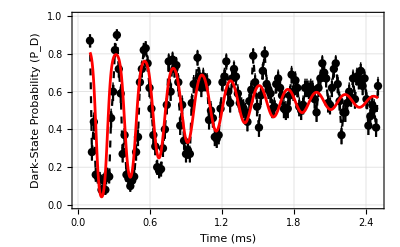
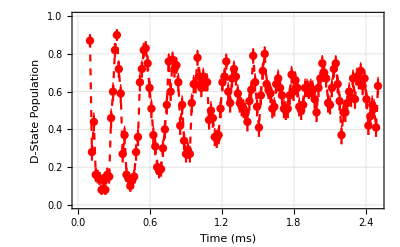

```mathematica
fitParams
summaryFigure
```

## tmp dont touch

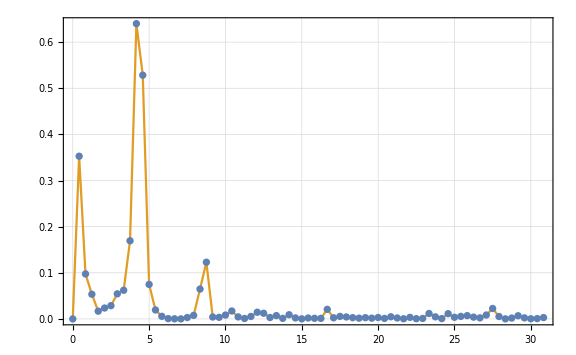

```mathematica
th0=dsN;
th0[[;;,2]]-=Mean[th0[[;;,2]]];
th0[[;;,2]]=#["Value"]&/@th0[[;;,2]];

th1x=Range[0,Length[th0]-1][[;;IntegerPart[Length[th0]/2.]]]*((1./(Length[th0]-1))/Mean[th0[[2;;-1,1]]-th0[[1;;-2,1]]]);
th1y=(Abs[Fourier[th0[[;;,2]]]]^2.)[[;;IntegerPart[Length[th0]/2.]]];
th2Plot=Transpose[{th1x,th1y}];
ListPlot[{th2Plot,th2Plot},Joined->{False,True},PlotRange->Full]
```

## Phaser Waveform Display

```mathematica
riddj=141479;
```

## Configuration

```mathematica
filenameDJ=FileNames["*"<>ToString[riddj]<>"*.h5",directoryString,Infinity];
datasetRaw=Import[First@filenameDJ,{"/datasets"}];
```

```mathematica
th0=KeySelect[datasetRaw,StringContainsQ[#,"phaser"]&];
```

```mathematica
th0//Keys
```

{_phaser_wav_0_ampls,_phaser_wav_0_phases,_phaser_wav_0_times}

```mathematica
th1t=Accumulate[datasetRaw["_phaser_wav_0_times"]]/1000.;
(*th1a=datasetRaw["_phaser_wav_0_CH0_ampls"];
th1p=datasetRaw["_phaser_wav_0_CH0_phases"];*)
th1a=datasetRaw["_phaser_wav_0_ampls"];
th1p=datasetRaw["_phaser_wav_0_phases"];
```

```mathematica
th2a=Transpose[{th1t,#}]&/@Transpose[th1a];
th2p=Transpose[{th1t,#}]&/@Transpose[th1p];
```

```mathematica
amplPlot=ListLinePlot[
th2a,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["Amplitude",{Black,Directive[15]}],None},
{
Style["Time (μs)",{Black,Directive[15]}],
Style["Waveform",{Black,Directive[15]}]
}
},
PlotLegends->Range[5],
ImageSize->Scaled[0.45]
];
```

```mathematica
phasPlot=ListLinePlot[
th2p,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["Phase",{Black,Directive[15]}],None},
{
Style["Time (μs)",{Black,Directive[15]}],
Style["Waveform",{Black,Directive[15]}]
}
},
PlotLegends->Range[5],
ImageSize->Scaled[0.45]
];
```

## Import

```mathematica
ch1rPlots={amplPlot,phasPlot};
```

```mathematica
sdrPlots={amplPlot,phasPlot};
```

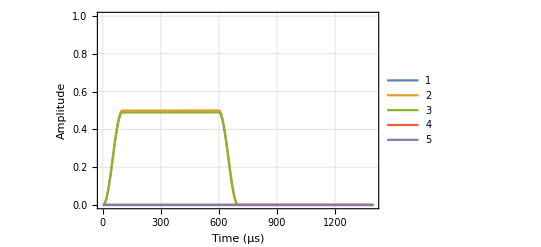
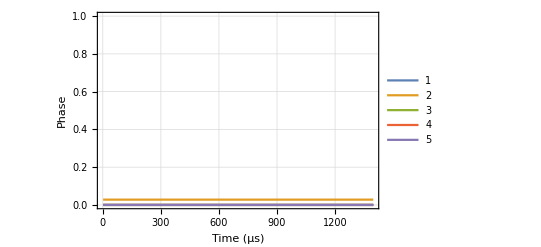

```mathematica
ch1rPlots
```

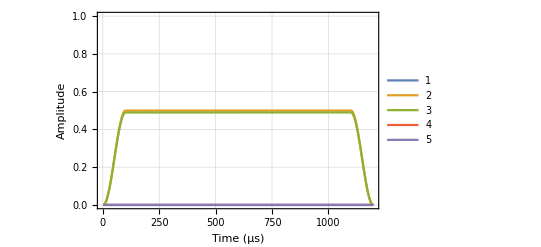
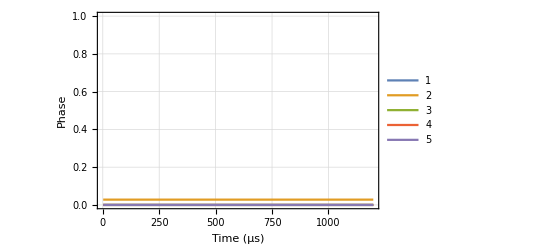

```mathematica
sdrPlots
```

## General Freq Sweep - (UNDER DEVELOPMENT)

```mathematica
rid=96585;
ϕ0=0.;
phaseCol=1;
holdoffCol=5;
```

```mathematica
holdoffIdx=1;
```

## Import

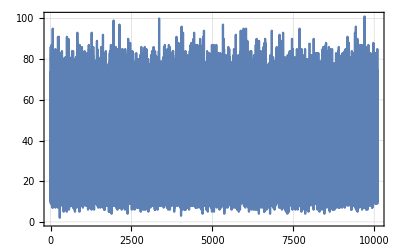
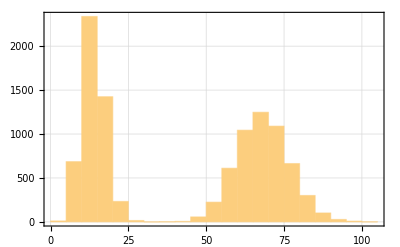
{(4.35228×10^8 | 13. | 2.×10^6 | 0. | 99999.
4.35229×10^8 | 10. | 2.×10^6 | 0. | 99999.
4.35227×10^8 | 70. | 2.×10^6 | 0. | 99999.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

```mathematica
(*extract important parameters*)
timeRamseyUS=First@parameters["time_delay_us_list"];
timePulseUS=parameters["time_pulse_us"];
phaseRamseyTurns=First@parameters["phase_ramsey_turns_list"];
holdoffTimesMU=(dataset[[;;,holdoffCol]]//DeleteDuplicates//Sort);
```

## Process

```mathematica
(*extract only points for a given holdoff time*)
dataset=Select[dataset,#[[holdoffCol]]==holdoffTimesMU[[holdoffIdx]]&];
```

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{phaseCol,2}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.}];
datasetProcessed=CollateData[datasetProcessed,{1}]//Values;
```

## Fit

### Complete Ramsey Fit

```mathematica
(*(*displace ramsey fit function*)
fitfunc=4. Ω^2. τ^2. Sinc[(2.*π)*((x-β)*τ)/2.+1.*^-5]^2. Sin[(2.*π)*(((x-β)*(T+τ))/2.+ϕ)]^2.+δ;
(*set fixed values*)
fitfunc=fitfunc/.{
τ->(timePulseUS(**1.*^-6*)),
T->(timeRamseyUS(**1.*^-6*)),
β->Mean[datasetProcessed[[;;,1]]]
(*ϕ->0.*)
};*)
```

```mathematica
(*(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc
},
{
{Ω,1.*^4},
{β,Mean[datasetProcessed[[;;,1]]]},
{τ,timePulseUS(**1.*^-6*)},
{T,timeRamseyUS(**1.*^-6*)},
{δ,Mean[datasetProcessed[[;;,2]]]},
{ϕ,0.}
},
x
];
]*)
```

### General Sine Fit

```mathematica
(*general sine fit*)
fitfunc=α*Cos[(2.*π)*(T)*(x-β)+ϕ]^2.+δ;

(*set fixed values*)
fitfunc=fitfunc/.{
T->(timeRamseyUS+timePulseUS)(**1.*^-6*),
ϕ->(2.*π)*phaseRamseyTurns
}
```

δ+α Cos[0.+12585.2 (x-β)]^2.

```mathematica
(*guess initial values*)
guessα=1.0*(Max[datasetProcessed[[;;,2]]]-Min[datasetProcessed[[;;,2]]]);
guessβ=Mean[datasetProcessed[[;;,1]]];
guessT=(timeRamseyUS+timePulseUS)(**1.*^-6*);
guessδ=Mean[datasetProcessed[[;;,2]]];
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
datasetProcessed,
{
fitfunc
},
Transpose[{
{α,β,T,δ},
{guessα,guessβ,guessT,guessδ}
}],
x
];
]
```

{0.0054475,Null}

### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[x],
{x,datasetProcessed[[1,1]],datasetProcessed[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
datasetProcessed,
datasetProcessed
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["P_(S - 1/2)",{Black,Directive[15]}],None},
{
Style["Frequency (MHz)",{Black,Directive[15]}],
Style["729nm Ramsey (T_Delay = "<>ToString[timeRamseyUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
fitPlot
]
};
```

## Show

(101.335065
0.
0.099999)

| Estimate | Standard Error | Confidence Interval
α | 0.301834 | 0.0118409 | {0.278333,0.325334}
β | 101.335 | 1.55513×10^-6 | {101.335,101.335}
T | 2003. | 0. | {2003.,2003.}
δ | 0.314237 | 0.00728254 | {0.299784,0.328691}

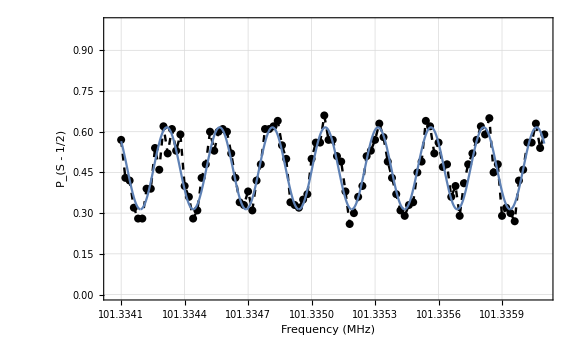

```mathematica
{NumberForm[fitParams[[1,1,3,2]],9],
phaseRamseyTurns,
holdoffTimesMU[[holdoffIdx]]/1.*^6}//MatrixForm
fitParams
summaryFigure
```

```mathematica
{0.0015,3.*^-5}*(1000.)*1000./3000.
```

{0.5,0.01}

```mathematica
Join[{timeRamseyUS},fitParams[[1,1,2,2;;]]]
```

{2000.,-0.268363,0.0135732,{-0.295302,-0.241424}}

# Bichromatic (wigner) phase sweep wrt QVSA

```mathematica
RandomSample[Range[0,1000,100]]
```

{600,800,900,200,300,400,0,100,1000,500,700}

```mathematica
rid=117186;
countCol=2;
phaseCol=4;
```

```mathematica
βCalib=3.653/50.;αCalib=20./500.;
guessαβ0=0.1*(βCalib)*(αCalib);
guessϕ=-0.25;
```

```mathematica
guessConstraints={
(*-1.<=A<1.,
-10.<=αβ<=10.*)
(*αβ==7.0,*)
(*1.<=A<=0.*)
(*-0.3<=δ<=0.,
-1.<=A<=-0.05*)
};
```

```mathematica
3.61157
```

3.61157

## TMP hide

## Import

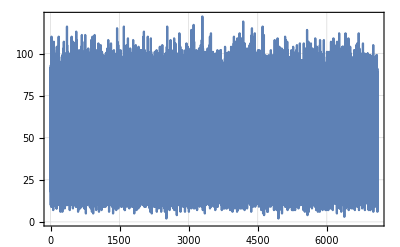
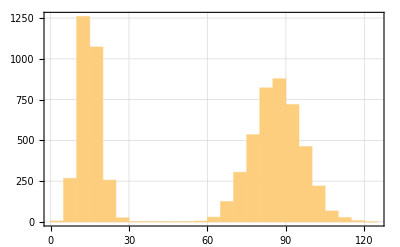
{(0. | 92. | 19999. | 16852.
0. | 82. | 19999. | 34640.
0. | 18. | 19999. | 9362.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

```mathematica
(*extract important parameters*)
timeQVSAUS=parameters["time_superresolution_stop_us"];
timeFullUS=parameters["time_eggs_heating_us"];
timeBichromaticUS=parameters["time_char_phase_sweep_us"];
(*todo: get PSK and num*)
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{phaseCol,countCol}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{1./(2^16-1.),1.}];
datasetProcessed=CollateData[datasetProcessed,{1}]//Values;
```

```mathematica
(*phase unwrap & sort*)
datasetProcessed[[;;,1]]=Mod[datasetProcessed[[;;,1]],1,-0.5];
datasetProcessed=SortBy[datasetProcessed,First];
```

## Fit

```mathematica
(*use dataset parameters to inform guess values*)
timeAdjustUS=timeQVSAUS-2.*UnitStep[(timeQVSAUS-1.)-timeFullUS/2]*Mod[timeQVSAUS,timeFullUS/2,0];(*adjusted time accounting for PSK*)
guessαβ=guessαβ0*timeAdjustUS*timeBichromaticUS
```

5.8448

### Coherent Fringes Fit

```mathematica
(*general sine fit*)
fitfunc=0.5*(1.+A*Cos[2.*αβ*Sin[(2.*π)*(θ-ϕ)]])+δ;
(*fitfunc=A*Cos[αβ*Sin[(2.*π)*(θ-ϕ)]]^2.+δ;*)
```

```mathematica
(*guess initial values*)
guessA=-1.*(Max[datasetProcessed[[;;,2]]]-Min[datasetProcessed[[;;,2]]])
guessδ=Mean[datasetProcessed[[;;,2]]]-0.5
```

-0.8

-0.0907143

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
datasetProcessed,
Join[{fitfunc},guessConstraints],
Transpose[{
{A,αβ,ϕ,δ},
{guessA,guessαβ,guessϕ,guessδ}
}],
θ,
MaxIterations->1*^6
];
]
```

{0.0008891,Null}

### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[x],
{x,datasetProcessed[[1,1]],datasetProcessed[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
datasetProcessed,
datasetProcessed
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["P_(D - 5/2)",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["QVSA vs Cat Phase (T_QVSA = "<>ToString[timeQVSAUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
fitPlot
]
};
```

## Show

```mathematica
guessαβ
```

5.8448

| Estimate | Standard Error | Confidence Interval
A | -0.65106 | 0.0138885 | {-0.678789,-0.62333}
αβ | 6.594 | 0.0181487 | {6.55776,6.63023}
ϕ | -0.267813 | 0.000369878 | {-0.268551,-0.267074}
δ | -0.0202843 | 0.00522282 | {-0.030712,-0.00985662}

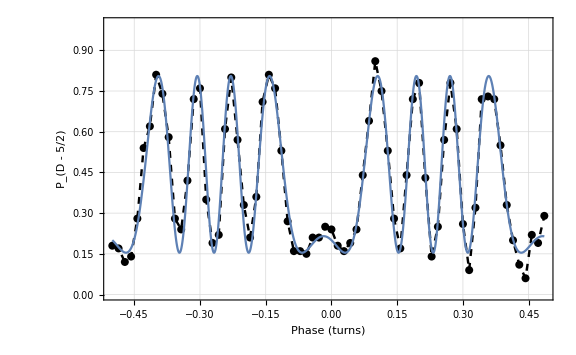

```mathematica
fitParams
summaryFigure
```

```mathematica
0.25-0.223305
```

0.026695

```mathematica
0.02828*360
```

10.1808

```mathematica
ArcTan[0.607337/4.03156]/(π/180.)
```

8.56694

```mathematica
ArcTan[1]/(π/180.)
```

45.

## plot summary

## Create Dataset

```mathematica
dsDJ={
{100,{-0.047234,0.00608},{0.974542,0.0363463}},
{200,{-0.00085,0.00299},{1.61851,0.0705}},
{300,{0.01165,0.0048931},{2.21492,0.0677491}},
{400,{-0.00811,0.001927},{2.7552,0.03894}},
{500,{-0.0066,0.001296},{3.7311,0.0313}},
{600,{0.00179,0.0017983},{3.11122,0.0515598}},
{700,{-0.003517,0.00297},{2.2909,0.0392868}},
{800,{0.000599644,0.00225},{1.71381,0.00297}},
{900,{0.028922,0.0056951},{0.833862,0.426588}}
(*{1000,{-0.0283,0.0033},{2.35274,0.0324992}}*)
};
(*mod phase values to [-0.5,0.5] (i.e. [-π,π])*)
(*dsDJ[[;;,2,1]]=Mod[dsDJ[[;;,2,1]],0.5,-0.25];
dsDJ[[8;;,2,1]]=Mod[dsDJ[[8;;,2,1]],0.5,0.];
dsDJ[[10;;,2,1]]=Mod[dsDJ[[10;;,2,1]],0.5,0.25];*)
(*dsDJ[[;;,2,1]]=Mod[dsDJ[[;;,2,1]],0.5,0.25];
dsDJ[[8;;,2,1]]=Mod[dsDJ[[8;;,2,1]],0.5,0.5];*)
(*dsDJ[[10;;,2,1]]=Mod[dsDJ[[10;;,2,1]],0.5,0.25];*)

(*create sub-datasets*)
dsϕ=Transpose[{dsDJ[[;;,1]],dsDJ[[;;,2,1]]}];
dsαβ=Transpose[{dsDJ[[;;,1]],dsDJ[[;;,3,1]]}];
```

## Create & Show Plots

{0.0005048,Null}

| Estimate | Standard Error | Confidence Interval
1 | 3.16374 | 1.03188 | {0.723733,5.60376}
t | -0.000578912 | 0.00186605 | {-0.00499142,0.0038336}

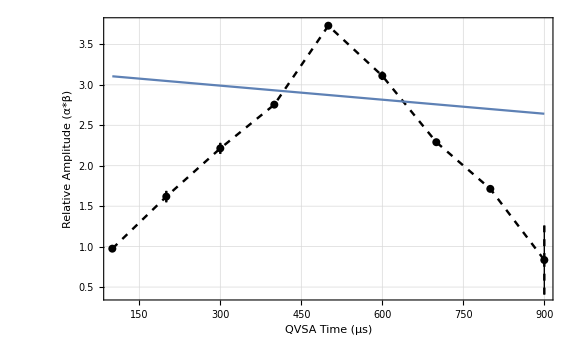

```mathematica
(*fit linear trend & plot*)
AbsoluteTiming[
ϕAmplFit=LinearModelFit[
dsαβ,
{1,t},
t,
Weights->(dsDJ[[;;,2,2]]/2)^-2
];
]
(*get fit params*)
ϕAmplParams=Style[
ϕAmplFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]
Show[
ListPlot[
{#,#},
PlotRange->{{Full,Full},{Full,Full}},
FrameLabel->{ 
{Style["Relative Amplitude (α*β)",{Black,Directive[15]}],None},
{
Style["QVSA Time (μs)",{Black,Directive[15]}],
Style["Fitted Product Amplitude",{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
Plot[
ϕAmplFit[t],
{t,dsαβ[[1,1]],dsαβ[[-1,1]]}
],
PlotRange->{{Full,Full},{Full,Full}}
(*]&[Transpose[{dsDJ[[;;,1]],dsDJ[[;;,3,1]]}]]*)
]&[Transpose[{dsDJ[[;;,1]],Around@@@dsDJ[[;;,3]]}]]
```

{0.0006928,Null}

| Estimate | Standard Error | Confidence Interval
1 | -0.0318383 | 0.00948619 | {-0.0542696,-0.00940701}
ϕ | 0.0000406591 | 0.000011989 | {0.0000123098,0.0000690085}

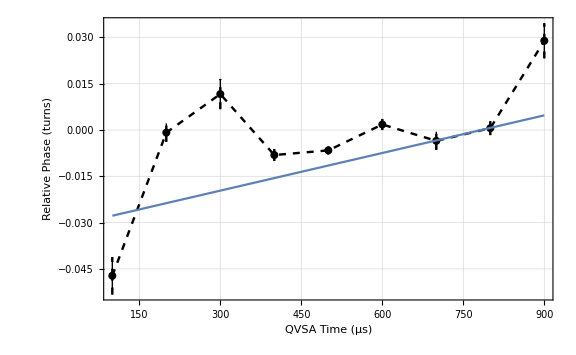

```mathematica
(*fit linear trend & plot*)
AbsoluteTiming[
ϕDriftFit=LinearModelFit[
dsϕ,
{1,ϕ},
ϕ,
Weights->(dsDJ[[;;,3,2]]/2)^-2
];]
(*get fit params*)
ϕDriftParams=Style[
ϕDriftFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]
Show[
ListPlot[
{#,#},
PlotRange->{{Full,Full},{Full,Full}},
FrameLabel->{ 
{Style["Relative Phase (turns)",{Black,Directive[15]}],None},
{
Style["QVSA Time (μs)",{Black,Directive[15]}],
Style["QVSA vs Cat Phase",{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
Plot[
ϕDriftFit[ϕ],
{ϕ,dsϕ[[1,1]],dsϕ[[-1,1]]}
],
PlotRange->{{Full,Full},{Full,Full}}
(*]&[Transpose[{dsDJ[[;;,1]],dsDJ[[;;,2,1]]}]]*)
]&[Transpose[{dsDJ[[;;,1]],Around@@@dsDJ[[;;,2]]}]]
```

# Deprecated

## SDR X2 freq sweep

```mathematica
rid=140809;
ϕ0=0.;
```

```mathematica
freqReadoutCol=1;
countCol=2;
freqSweepCol=4;
phaseSweepCol=5;
```

## Import

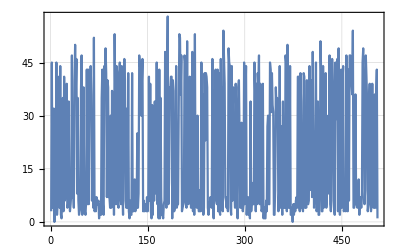
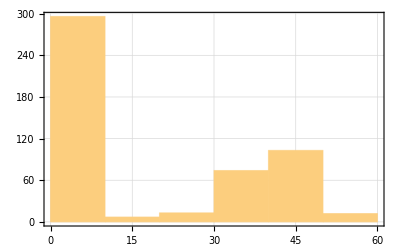
{(-1. | 3. | 3.5×10^8 | -170. | 0. | 200. | 1. | 0. | 256. | 0.
-1. | 45. | 3.5×10^8 | -30. | 0. | 200. | 1. | 0. | 256. | 0.
-1. | 2. | 3.5×10^8 | 250. | 0. | 200. | 1. | 0. | 256. | 0.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;;;50]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#[[;;;;50]],ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

```mathematica
(*ds0=dataset;
(*dataset[[;;,5]]-=0;*)
th0=GroupBy[dataset,#[[5]]&]//KeySort;*)
```

```mathematica
(*dataset=th0[[#]]&[6];*)
```

```mathematica
(*th0[[6;;]]//Keys*)
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{freqReadoutCol,freqSweepCol,phaseSweepCol,countCol}]],4];
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{ftwToFrequencyMHz,1.*^-0,1.*^-0,1}
];
freqCenter=Mean[datasetProcessed[[;;,1]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,4}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,4}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

Thread::tdlen: Objects of unequal length in {}/{0.904,0.896,0.876,0.9,0.9,0.908,0.916,0.916,0.936,0.884,«91»} cannot be combined.

```mathematica
(*tmp fix*)
dsN[[;;,1]]+=1.*^-7;
```

## Fit

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
A*x^k+B
},
{
{A,1.4},
{k,2.5},
{B,0.}
},
x
];
]
```

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

{0.0173486,Null}

### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,1⟧ in {ϕ,{}⟦1,1⟧,{}⟦-1,1⟧} is not a machine-sized real number.

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
dsN,
dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,Full}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["SuperRes - X2 Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True},
ImageSize->Scaled[0.45]
],
fitPlot
],
ListPlot[
{
dsR,
dsB
},
PlotRange->{
{Automatic,Automatic},
{0.,1.0}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["SuperRes - X2 Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black},
ImageSize->Scaled[0.45]
]
};
```

Show::gcomb: Could not combine the graphics objects in Show[,Plot[fitRes[ϕ],{ϕ,dsN⟦1,1⟧,dsN⟦-1,1⟧}]].

ListPlot::lpn: {{},{{-500.,0.904},{-490.,0.896},{-480.,0.876},{-470.,0.9},{-460.,0.9},{-450.,0.908},{-440.,0.916},{-430.,0.916},{-420.,0.936},{-410.,0.884},«91»}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[fitRes[ϕ],{ϕ,dsN⟦1,1⟧,dsN⟦-1,1⟧}]].

## Show

```mathematica
fitParams
summaryFigure
```

ParameterConfidenceIntervalTable

{Show[-Graphics-,Plot[fitRes[ϕ],{ϕ,dsN⟦1,1⟧,dsN⟦-1,1⟧}]],ListPlot[{{},{{-500.,0.904},{-490.,0.896},{-480.,0.876},{-470.,0.9},{-460.,0.9},{-450.,0.908},{-440.,0.916},{-430.,0.916},{-420.,0.936},{-410.,0.884},{-400.,0.904},{-390.,0.9},{-380.,0.924},{-370.,0.908},{-360.,0.932},{-350.,0.92},{-340.,0.888},{-330.,0.904},{-320.,0.928},{-310.,0.932},{-300.,0.884},{-290.,0.92},{-280.,0.86},{-270.,0.848},{-260.,0.812},{-250.,0.836},{-240.,0.82},{-230.,0.732},{-220.,0.74},{-210.,0.604},{-200.,0.572},{-190.,0.556},{-180.,0.472},{-170.,0.4},{-160.,0.356},{-150.,0.296},{-140.,0.272},{-130.,0.196},{-120.,0.16},{-110.,0.156},{-100.,0.116},{-90.,0.096},{-80.,0.056},{-70.,0.052},{-60.,0.032},{-50.,0.064},{-40.,0.052},{-30.,0.04},{-20.,0.028},{-10.,0.04},{0.,0.036},{10.,0.02},{20.,0.044},{30.,0.052},{40.,0.012},{50.,0.012},{60.,0.028},{70.,0.068},{80.,0.052},{90.,0.08},{100.,0.084},{110.,0.144},{120.,0.168},{130.,0.22},{140.,0.284},{150.,0.316},{160.,0.44},{170.,0.372},{180.,0.484},{190.,0.544},{200.,0.64},{210.,0.688},{220.,0.696},{230.,0.712},{240.,0.748},{250.,0.852},{260.,0.836},{270.,0.828},{280.,0.908},{290.,0.912},{300.,0.872},{310.,0.896},{320.,0.9},{330.,0.924},{340.,0.924},{350.,0.92},{360.,0.904},{370.,0.916},{380.,0.92},{390.,0.948},{400.,0.936},{410.,0.876},{420.,0.908},{430.,0.932},{440.,0.92},{450.,0.92},{460.,0.884},{470.,0.928},{480.,0.88},{490.,0.944},{500.,0.912}}},PlotRange→{{Automatic,Automatic},{0.,1.}},FrameLabel→{{D-State Population,None},{Frequency (Hz),SuperRes - X2 Sweep
RID: 140809}},PlotStyle→{RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[0]},ImageSize→Scaled[0.45]]}

## batch in small groups

```mathematica
(*group dataset for each freq*)
batchData=GroupBy[datasetProcessed,#[[2]]&]//KeySort;
```

### Group In Small Batches

```mathematica
(*process data in fixed batches - separately process freq/phase*)
KKFunc[data_,batchSize_]:=Module[
{
freqDiff=Mean[data[[;;,1]]],
sc1,scR,scB,scR2,scB2
},

sc1=GroupBy[data,#[[1]]<freqDiff&];
scR=sc1[True];
scB=sc1[False];

scR2=(Mean/@ArrayReshape[
scR[[;;IntegerPart[Length[scR]/batchSize]*batchSize]],
{IntegerPart[Length[scR]/batchSize],batchSize,Dimensions[scR][[2]]}
])[[;;,4]];
scB2=(Mean/@ArrayReshape[
scB[[;;IntegerPart[Length[scB]/batchSize]*batchSize]],
{IntegerPart[Length[scB]/batchSize],batchSize,Dimensions[scB][[2]]}
])[[;;,4]];
Return[Mean@(CoherentC[scR2/(scB2+1.*^-7)])];
];
```

```mathematica
(*dsBatch2N=Transpose[
{
Keys[batchData],
KKFunc[#,2]&/@Values[batchData]
}
];*)
```

```mathematica
(*dsBatch5N=Transpose[
{
Keys[batchData],
KKFunc[#,5]&/@Values[batchData]
}
];*)
```

```mathematica
(*dsBatch10N=Transpose[
{
Keys[batchData],
KKFunc[#,10]&/@Values[batchData]
}
];*)
```

### Group By Phase

```mathematica
(*process data in fixed batches - separately process freq/phase*)
KKFuncPhase[data_]:=Module[
{
freqDiff=Mean[data[[;;,1]]],
sc1,scR,scB,scR2,scB2
},

sc1=GroupBy[data,#[[1]]<freqDiff&];
scR=sc1[True];
scB=sc1[False];

scR2=(Mean/@(GroupBy[scR,#[[3]]&]//KeySort//Values))[[;;,4]];
scB2=(Mean/@(GroupBy[scB ,#[[3]]&]//KeySort//Values))[[;;,4]];
Return[Mean@(CoherentC[scR2/(scB2+1.*^-7)])];
];
```

```mathematica
dsPhaseN=Transpose[
{
Keys[batchData],
KKFuncPhase[#]&/@Values[batchData]
}
];
```

### Single-Point Measurement - RSB Only

```mathematica
freqDiff=Mean[datasetProcessed[[;;,1]]];
dsSPRSB=Select[datasetProcessed,#[[1]]<freqDiff&];
dsSPRSB=GroupBy[dsSPRSB,#[[2]]&]//KeySort;
```

```mathematica
(*process data in fixed batches - separately process freq/phase*)
KKFuncSPRSB[data_]:=Module[
{
freqDiff=Mean[data[[;;,1]]],
scR,scR2
},
scR=Select[data,#[[1]]<freqDiff&][[;;,4]];
Return[CoherentR[Mean@scR]];
];
```

```mathematica
dsSPRSBN=Transpose[
{
Keys[batchData],
KKFuncSPRSB[#]&/@Values[batchData]
}
];
```

## tmp remove 2

```mathematica
(*dsMeanIdealN=dsN;
dsMeanIdealN[[;;,2]]/=2.;*)
```

```mathematica
(*dsMinN=dsN;
dsMinR=dsR;
dsMinB=dsB;*)
```

```mathematica
(*dsMeanN=dsMaxN;
dsMeanN[[;;,2]]/=2.;*)
```

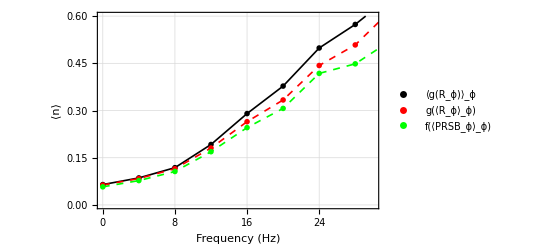

```mathematica
ListPlot[
{
dsPhaseN,dsPhaseN,
dsAllN,dsAllN,
dsSPRSBN,dsSPRSBN
},
PlotRange->{
{Automatic,30.},{0.,0.6}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["Estimator Comparison\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotLegends->{
"⟨g(R_ϕ)⟩_ϕ",None,
"g(⟨R_ϕ⟩_ϕ)",None,
"f(⟨PRSB_ϕ⟩_ϕ)",None
},
PlotStyle->{
{Black,PointSize[0.01]},{Black,Thickness[0.003]},
{Red,PointSize[0.01]},{Red,Dashed,Thickness[0.003]},
{Green,PointSize[0.01]},{Green,Dashed,Thickness[0.003]},
{Blue,PointSize[0.01]},{Blue,Dashed,Thickness[0.003]}
},
Joined->{
False,True,
False,True,
False,True,
False,True
},
ImageSize->Scaled[0.45]
]
```

## SDR Estimator comparison tmp

## tmp remove

```mathematica
(*(*readout freq, x2 freq, phase*)
datasetProcessedTMP=ThresholdCounts[dataset[[;;,{1,4,5,countCol}]],4];
batchData=GroupBy[datasetProcessedTMP,#[[2]]&]//KeySort;*)
```

```mathematica
(*KKFunc[data_,batchSize_]:=Module[
{
freqDiff=Mean[data[[;;,1]]],
sc1,scR,scB,scR2,scB2
},

sc1=GroupBy[data,#[[1]]<freqDiff&];
scR=sc1[True];
scB=sc1[False];

scR2=(Mean/@ArrayReshape[
scR[[;;IntegerPart[Length[scR]/batchSize]*batchSize]],
{IntegerPart[Length[scR]/batchSize],batchSize,Dimensions[scR][[2]]}
])[[;;,4]];
scB2=(Mean/@ArrayReshape[
scB[[;;IntegerPart[Length[scB]/batchSize]*batchSize]],
{IntegerPart[Length[scB]/batchSize],batchSize,Dimensions[scB][[2]]}
])[[;;,4]];
Return[Mean@(CoherentC[scR2/(scB2+1.*^-7)])];
];*)
```

```mathematica
dsBatch2N=Transpose[
{
Keys[batchData],
KKFunc[#,2]&/@Values[batchData]
}
];
```

```mathematica
(*dsBatch5N=Transpose[
{
Keys[batchData],
KKFunc[#,5]&/@Values[batchData]
}
];*)
```

```mathematica
(*dsBatch10N=Transpose[
{
Keys[batchData],
KKFunc[#,10]&/@Values[batchData]
}
];*)
```

## tmp remove 2

```mathematica
(*dsMeanIdealN=dsN;
dsMeanIdealN[[;;,2]]/=2.;*)
```

```mathematica
(*dsMinN=dsN;
dsMinR=dsR;
dsMinB=dsB;*)
```

```mathematica
(*dsMaxN=dsN;
dsMaxR=dsR;
dsMaxB=dsB;*)
```

```mathematica
(*dsAllN=dsN;
dsAllR=dsR;
dsAllB=dsB;*)
```

```mathematica
(*dsMeanN=dsMaxN;
dsMeanN[[;;,2]]/=2.;*)
```

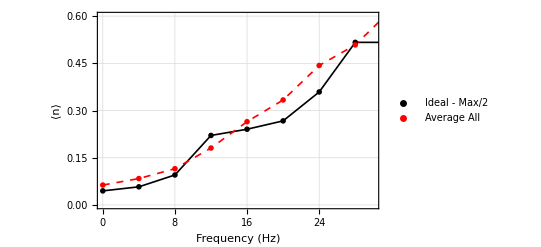

{1.35486,Null}

```mathematica
ListPlot[
{
(*dsMeanIdealN,dsMeanIdealN,*)
dsMeanN,dsMeanN,
dsAllN,dsAllN
(*dsBatch2N,dsBatch2N,
dsBatch5N,dsBatch5N*)
(*dsBatch10N,dsBatch10N*)
},
PlotRange->{
{Automatic,30.},
{0.,0.6}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["Estimator Comparison\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotLegends->{
"Ideal - Max/2",None,
"Average All",None,
"Batched - 2 Points",None,
"Batched - 5 Points",None
},
PlotStyle->{
{Black,PointSize[0.01]},{Black,Thickness[0.003]},
{Red,PointSize[0.01]},{Red,Dashed,Thickness[0.003]},
{Green,PointSize[0.01]},{Green,Dashed,Thickness[0.003]},
{Blue,PointSize[0.01]},{Blue,Dashed,Thickness[0.003]}
},
Joined->{
False,True,
False,True,
False,True,
False,True
},
ImageSize->Scaled[0.45]
]
```